# Unit 4 - Limits and the Graphics Objects

This unit covers the following topics.

Review

Using tables to exam the existence of limits

Limit - The Mathematica function; Module

Identifying vertical and horizontal asymptotes

Finding the derivative by definition

Graphics objects and operations

## Review

First, let us brief review the definition of the limit of a function. Given that f(x) is a function defined at least on an open interval containing x_0 except possibly at x_0, we say that the limit of f(x) at x_0

limit_(x→x_o)f(x)=L

if for any arbitrary ε>0, there exists at least one δ>0 such that if 0<|x-x_0|<δ then |f(x)-L|<ε.

In the this definition, x approaches x_0 both from sides of x_0. How about if x approaches x_0 just from one side?

If f(x) is defined at least on an open interval with x_0 as its right endpoint. We say that the left-hand limit of f(x) at x_0

limit_(x→x_0^-)f(x)=L

if for any arbitrary ε>0, there exists at least one δ>0 such that if 0<x_0-x<δ then |f(x)-L|<ε.

Similarly, if f(x) is defined at least on an open interval with x_0 as its left endpoint, we say that the right-hand limit of f(x) at x_0

limit_(x→x_0^+)f(x)=L

if for any arbitrary ε>0, there exists at least one δ>0 such that if 0<x-x_0<δ then |f(x)-L|<ε.

We know that limit_(x→x_o)f(x)=L if and only if limit_(x→x_0^-)f(x)=L and limit_(x→x_0^+)f(x)=L.
In addition, we say f(x) is continuous at x_0 if limit_(x→x_o)f(x)=f(x_o), i.e., 1) the limit of f(x) at x_0 exists; 2) f(x) is defined at x_0; 3) f(x_0) and the limit of f(x) at x_0 are equal. If there is at least one of the three conditions which is not met, f(x) is discontinuous at x_0.

## Using tables to exam the existence of limits

Before using Mathematica built-in function Limit to find limiting value, we first construct a table of the coordinates of x and f(x) and use it to exam the existence of a limit at a point. One of the most famous limits is certainly limit_(x→0) (sin x)/x =1.

We should know that, due to the constraints of hardware, no computer can assume an arbitrarily small quantity. Therefore, in this unit when we exam the existence of a limit by constructing tables around x_0, we will do experiment with the increment in x which is small but not arbitrarily small.

Example 1
Use graph and a table to exam the existence of the limit of (sin x)/xat x=0.

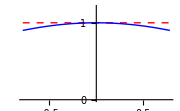

x | Sin[x]/x
-1.1 | 0.810189
-0.9 | 0.870363
-0.7 | 0.920311
-0.5 | 0.958851
-0.3 | 0.985067
-0.1 | 0.998334
0.1 | 0.998334
0.3 | 0.985067
0.5 | 0.958851
0.7 | 0.920311
0.9 | 0.870363
1.1 | 0.810189 | x | Sin[x]/x
-0.11 | 0.997985
-0.09 | 0.998651
-0.07 | 0.999184
-0.05 | 0.999583
-0.03 | 0.99985
-0.01 | 0.999983
0.01 | 0.999983
0.03 | 0.99985
0.05 | 0.999583
0.07 | 0.999184
0.09 | 0.998651
0.11 | 0.997985 | x | Sin[x]/x
-0.011 | 0.99998
-0.009 | 0.999987
-0.007 | 0.999992
-0.005 | 0.999996
-0.003 | 0.999999
-0.001 | 1.
0.001 | 1.
0.003 | 0.999999
0.005 | 0.999996
0.007 | 0.999992
0.009 | 0.999987
0.011 | 0.99998

```mathematica
Clear[x]
g[x_]:=Sin[x]/x
f[x_]:=N[g[x],8]
Plot[{1,f[x]},{x,-π/4,π/4},PlotRange->{0,1.2},PlotStyle->{{Red, Dashed},{Blue}},Ticks->{{-0.5,0,0.5},{0,0.5,1}},ImageSize->180]
Grid[{
Map[TableForm,{
Join[{{x,g[x]}},Table[{x,f[x]},{x,-1.1,1.1,0.2}]],(* choose values so as to prevent x from taking 0 *)
Join[{{x,g[x]}},Table[{x,f[x]},{x,-0.11,0.11,0.02}]],(* each Table here has the same size *)
Join[{{x,g[x]}},Table[{x,f[x]},{x,-0.011,0.011,0.002}]]
}]
},Spacings->3]
```

From both the graph and the table, we can see that the values of f(x) converge to 1 as x approaches 0 from either side. Therefore, the limit of (sin x)/xis possibly 1 at x=0. Note: this approach is far from a rigorous proof.

Another example is the fact, limit_(x→∞) (1+1/x)^x =ⅇ≈2.71828. Again, technically, no computer can take an arbitrarily large quantity. We can only test on some large numbers.

Example 2
Use graph and a table to exam the existence of the limit of (1+1/x)^x at infinity.

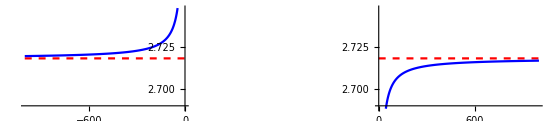

x | (1+1/x)^x
-100000 | 2.7182954
-90000 | 2.7182969
-80000 | 2.7182988
-70000 | 2.7183012
-60000 | 2.7183045
-50000 | 2.718309
-40000 | 2.7183158
-30000 | 2.7183271
-20000 | 2.7183498
-10000 | 2.7184178 | x | (1+1/x)^x
-10000 | 2.7184178
-9000 | 2.7184329
-8000 | 2.7184517
-7000 | 2.718476
-6000 | 2.7185084
-5000 | 2.7185537
-4000 | 2.7186217
-3000 | 2.718735
-2000 | 2.7189617
-1000 | 2.7196422 | x | (1+1/x)^x
1000 | 2.7169239
2000 | 2.7176026
3000 | 2.7178289
4000 | 2.7179421
5000 | 2.7180101
6000 | 2.7180553
7000 | 2.7180877
8000 | 2.718112
9000 | 2.7181308
10000 | 2.7181459 | x | (1+1/x)^x
10000 | 2.7181459
20000 | 2.7182139
30000 | 2.7182365
40000 | 2.7182479
50000 | 2.7182546
60000 | 2.7182592
70000 | 2.7182624
80000 | 2.7182648
90000 | 2.7182667
100000 | 2.7182682

```mathematica
Clear[x]
g[x_]:=(1+1/x)^x
f[x_]:=N[g[x],8]
GraphicsRow[{ (* to be covered in the last section of this unit *)
Plot[{E,f[x]},{x,-1000,0},PlotRange->{E-0.03,E+0.03},PlotStyle->{{Red,Dashed},{Blue}}],
Plot[{E,f[x]},{x,0,1000},PlotRange->{E-0.03,E+0.03},PlotStyle->{{Red,Dashed},{Blue}}]
},Spacings->290,ImageSize->550]
Grid[{
Map[TableForm,{
Join[{{x,g[x]}},Table[{x,f[x]},{x,-100000,-10000,10000}]],(* each Table here has the same size *)
Join[{{x,g[x]}},Table[{x,f[x]},{x,-10000,-1000,1000}]],
Join[{{x,g[x]}},Table[{x,f[x]},{x,1000,10000,1000}]],
Join[{{x,g[x]}},Table[{x,f[x]},{x,10000,100000,10000}]]
}]
},Spacings->3]
```

This table indicates that f(x) becomes close to ⅇ≈2.71828 as x goes to either negative or positive infinite.

## Limit - The Mathematica function

The Mathematica function for finding the limit of a function f(x) at x_0 is Limit. It can find one-sided limit through the option Direction.

Usage: Limit[expr,x→x_0], finding the limiting value of expr when x approaches x_0.
Option: Direction→1, finding left-hand limit;
              Direction→-1, finding right-hand limit

Example 3
Find the two one-sided limits of f(x)=Piecewise[{{1/x ⅇ^x,, x≠0}, {5, x=0}}] at x=0.

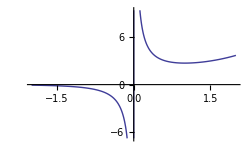

```mathematica
f[x_]:=Piecewise[{{1/x ⅇ^x,x≠0},{5,x==0}}]
Plot[f[x],{x,-2,2},ImageSize->250]
```

```mathematica
Limit[f[x],x->0,Direction->-1]
```

∞

```mathematica
Limit[f[x],x->0,Direction->1]
```

-∞

At x=0, since the two one-sided limits are not equal, the limit off(x) does not exist, and f(x)  is discontinuous.

If no option Direction is given, Limit assumes that Direction→-1 is the missing option. In other words, by default, Limit finds the right-hand limit. For example,

```mathematica
Limit[f[x],x->∞]
```

∞

We can define a function for finding limit as what we expected in calculus as follows.

```mathematica
FindLimit[f_,xtoa_]:=Module[{lLimit,rLimit},
lLimit=Limit[f,xtoa,Direction->1];
rLimit=Limit[f,xtoa,Direction->-1];
If[lLimit==rLimit,lLimit,"Limit doesn't exist."]]
```

```mathematica
FindLimit[f[x],x->0]
```

Limit doesn't exist.

```mathematica
FindLimit[f[x],x->1]
```

ⅇ

The command Module is a good and almost necessary tool for us to keep Mathematica workspace from being messed up. When we develop lengthy and complicated code, it is the primary mechanism leading to success. Another similar command is Block. (See Unit 6 for the difference between Module and Block.)

Usage: Module[{local symbols}, command]
If command consists of multiple commands, we can place the commands into a list; but the typical practice is using semicolon “;” to separate commands instead of creating a list. The result of the last command in a Module is the output of that Module. For example, Module[{x=4},√x; 2x]  gives 8. However, in Module[{x=4},{√x, 2x}], {√x, 2x} is the last command and, thus, {2, 8} is the output of this Module.

The Module command is similar to a list in the sense that, in a Module command, we can embed other Module commands. Symbols defined outside all Module commands at the first level in all cells are said to be global; symbols defined in the first argument of a Module command, a list of symbols, are said to be local. A global symbol can be accessed by every command in all opened notebooks in a Mathematica session, but a local symbol can only be accessed by commands inside the very Module command, including commands inside its embedded Module commands.

For example, in our example, f(x) and FindLimit are global, while lLimit and rLimit are local. The next example shows how to use global and local symbols. If you can determine all outputs correctly, you have mastered how to use Module.

```mathematica
f[x_]:=x(* f, g, and course are global *)
g[x_]:=2x
course=131;

value=Module[{g,course=133, limit, tmp},(* g, course, and limit are local to this Module; local symbols g and course hide the corresponding global ones *)
g[x_]:=3x;
limit = Limit[f[x],x->1];
Print[course];
Print[limit];
Print[g[1]];

tmp = Module[{g, result},(* g and result are local to this Module; this g hides the local g defined in the exterior Module *)
g[x_]:=4x;
result=g[1];
Print[result];
Print[limit];
100*f[1] (* the result of this last command of Module is the result returned from Module *)
]; (* end of interior Module *)

Print[tmp];
Print[f[1]];
Print[g[1]];
Print[result];(* cannot access local variable defined in the interior Module *)
]; (* end of exterior Module *)

Print[result];(* cannot access local variable defined in a Module *)
Print[limit];(* cannot access local variable defined in a Module *)
Print[g[1]]
Print[course]
```

133

1

3

4

1

100

1

3

result

result

limit

2

131

If we use semicolon to separate commands in a Module command, the output of each command except the last one is filtered out. When testing and debugging our code, we often want to see what happens at some point of the code before the last command and make sure everything is correct, e.g., a variable is assigned to an expected value, before that point. In this case, we may insert a Print command to print our the value of the variable. Multiple Print commands may be inserted into the code if needed. After all debugging work is done, we remove all Print commands for this purpose.

For example, we are supposed to get the result 3.14159 by evaluating √10+sin √10. We might first have the following code.

```mathematica
Module[{x=10,tmp},
tmp=√(x^2);
tmp+Sin[tmp]]//N
```

9.45598

What is wrong with the code? It seems everything is correct. Now, we want to check if the command before the last one produces correct answer. We can do so by inserting a Print command after that command as follows.

```mathematica
Module[{x=10,tmp},
tmp=√(x^2);
Print["tmp = ", tmp];
tmp+Sin[tmp]]//N
```

tmp = 10

9.45598

Now, we know this is incorrect, which enables us to focus on the command, tmp=√(x^2), and find the mistake, √xwas somehow typed as √(x^2). Correct the mistake,

```mathematica
Module[{x=10,tmp},
tmp=√x;
Print["tmp = ", tmp];
tmp+Sin[tmp]]//N
```

tmp = √10

3.14159

It works now! We finally remove the unnecessary Print command.

```mathematica
Module[{x=10,tmp},
tmp=√x;
tmp+Sin[tmp]]//N
```

3.14159

This example is really simple. However, when you develop lengthy Mathematica code, this debugging technique will be your basic and favorite tool.

## Identifying vertical and horizontal asymptotes

For a function f(x), if limit_(x→x_0^+)f(x)=±∞ or limit_(x→x_0^-)f(x)=±∞, then x=x_0 is a vertical asymptote; if limit_(x→∞)f(x)=L_1 and/or limit_(x→-∞)f(x)=L_2, where L_1 and L_2 are constants, then y=L_1 and/or y=L_2 are horizontal asymptotes.

Example 4
Find the asymptotes of f(x)=(x^2+3x-10)/((x-1)(x+3)).
By algebra, we know the domain of f(x) is all real number set except x=-3,1 where f(x) is undefined because its denominator is zero. We can verify that x=-3 and x=1 are two vertical asymptotes of f(x) as follows.

```mathematica
f[x_]:=(x^2+3x-10)/((x-1)(x+3))
```

```mathematica
{Limit[f[x],x->-3,Direction->-1],Limit[f[x],x->-3,Direction->1]}
```

{∞,-∞}

```mathematica
{Limit[f[x],x->1,Direction->-1],Limit[f[x],x->1,Direction->1]}
```

{-∞,∞}

On the other hand, because

```mathematica
{Limit[f[x],x->∞],Limit[f[x],x->-∞]}
```

{1,1}

y=1 is the only horizontal asymptote of f(x). The graph of the function below confirms our conclusions.

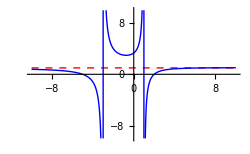

```mathematica
Plot[{1,f[x]},{x,-10,10},PlotStyle->{{Red,Dashed},{Blue}},PlotRange->{-10,10},ImageSize->250]
```

Example 5
Find the asymptotes of g(x)=Piecewise[{{2(1+x)^(1/x), x>0}, {-(x^2-x+3)/(x^2+1), x≤0}}].

By algebra, g(x) is defined on the entire real number set. Thus, there is no vertical asymptote. We will see if there are any horizontal asymptotes.

```mathematica
g[x_]:=If[x>0,2(1+x)^(1/x),-(x^2-x+3)/(x^2+1)]
{Limit[g[x],x->∞],Limit[g[x],x->-∞]}
```

{2,-1}

Therefore, y=-1 and y=2 are two horizontal asymptotes. The graph of g(x) confirms the conclusions.

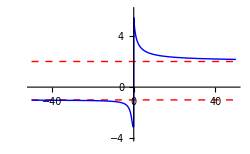

```mathematica
Plot[{-1,2,g[x]},{x,-50,50},PlotStyle->{{Red,Dashed},{Red,Dashed},{Blue}},PlotRange->{-4,6},ImageSize->250]
```

## Finding the derivative by definition

By definition, if the limit limit_(h→0)(f(a+h)-f(a))/hexists, f(x) is said to be differentiable at x=a, and the limit is called the derivative of f(x) at x=a, denoted by f'(a).

Example 6
Given that f(x)=ϵ^(2x)sin x, find f'(x) and f'(π/2).

```mathematica
f[x_]:=ⅇ^(2x)Sin[x]
Limit[(f[x+h]-f[x])/h,h->0]
```

ⅇ^(2 x) (Cos[x]+2 Sin[x])

```mathematica
%/.x->π/2
```

2 ⅇ^π

## Graphics objects and operations

Mathematica provides a rich set of Graphics objects. Plot, ContourPlot, ParametricPlot, PolarPlot, VectorPlot, and so on, each generate a Graphics object as complicated as needed. We may also use basic components, such as Text, Line, Point, Rectangle, Circle, Disk, and so on, to create simple Graphics objects in the way like Graphics[Text[f(x), {-1, 1}], Graphics[{Red,Text[f(x),{-1,1}}], and Graphics[{Red,PointSize[Medium],Point[{0.1,0.13}]}]. Each basic component can be customized with so-called directives, such as PointSize (for Point) and Arrowheads (for Arrow).

We will study and use many of these Graphics objects throughout the eleven units of this program. In particular, we will study ContourPlot in Unit 6, ParametricPlot and PolarPlot in Unit 10, and VectorPlot in Unit 11.

In this section, we are to study how to create a complicated graph and how to organize graphs.

1. To merge multiple Graphics objects into one graph:  Show [{GraphicsObj_1,GraphicsObj_2,⋯}];

2. To show Graphics objects in a row:                                    GraphicsRow [{GraphicsObj_1,GraphicsObj_2,⋯}];

3. To show Graphics objects in a column:                            GraphicsColumn [{GraphicsObj_1,GraphicsObj_2,⋯}];

4. To organize Graphics objects in rows and columns:   GraphicsGrid [{{GraphicsObj_row1_1,⋯},{GraphicsObj_row2_1,⋯},⋯}].

The result returned by Show, GraphicsRow, GraphicsColumn, and GraphicsGrid is still a Graphics object.

In brief, Mathematica provides the potential for us to create graphs we want. Here are some examples.

Show, merging multiple Graphics objects into one graph

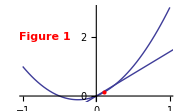

```mathematica
Show[{
Plot[x+2x^2,{x,-1,1},ImageSize->180],
ParametricPlot[{2t,3t},{t,-1,1}],
Graphics[{Red,Text[Style["Figure 1",Italic,Bold],{-0.7,2}]}],
Graphics[{Red,PointSize[Medium],Point[{0.1,0.13}]}]
}]
```

We use Show to combine or merge multiple Graphics objects into one single graph. The first plot object in the list of Show is usually used to set up the frame size and the look of the merged graph. For example,

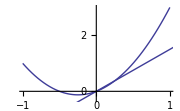

```mathematica
Show[{
Plot[x+2x^2,{x,-1,1},PlotRange->{-0.3,3},ImageSize->180],
Plot[3/2 x,{x,-5,10},PlotRange->{-5,5}](* this domain and this PlotRange do not matter! *)
}]
```

We use Show to combine or merge multiple Graphics objects into one single graph. The first plot object in the list of Show[{⋯}] is usually used to set up the frame size and the look of the merged graph. And the positions of Graphics objects in the list matter since a latter one will be put on top of any former one. For examples,

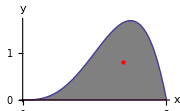

```mathematica
Show[{
Plot[x,{x,0,2},PlotRange->{0,1.7},PlotStyle->White,Ticks->{{0,1,2},{0,1}},AxesLabel->{x,y},ImageSize->180],
(* Often we have to let the first Plot do nothing but set up the frame size and the look of the graph. PlotStyle->White is just a necessary trick! *)

Plot[{2 x^3-x^4,0},{x,0,2},Filling->Axis,FillingStyle->Gray],
Graphics[{Red,PointSize[Large],Point[{1.4,0.8}]}] (* a red dot is on top of the shaded region *)
}]
```

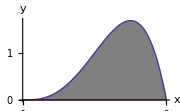

```mathematica
Show[{
Plot[x,{x,0,2},PlotRange->{0,1.7},PlotStyle->White,Ticks->{{0,1,2},{0,1}},AxesLabel->{x,y},ImageSize->180],
Graphics[{Red,PointSize[Large],Point[{1.4,0.8}]}], (* the same red dot *)Plot[{2 x^3-x^4,0},{x,0,2},Filling->Axis,FillingStyle->Gray] (* this shaded region is on top of the red dot *)
}]
```

GraphicsRow, showing Graphics objects in a row

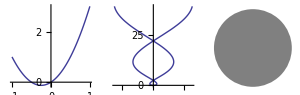

```mathematica
GraphicsRow[{
Plot[x+2x^2,{x,-1,1}],
ParametricPlot[{2t Cos[t],t^2},{t,-2Pi,2Pi}],
Graphics[{Gray,Disk[{0,1},1]}]
},ImageSize->300]
```

GraphicsColumn , showing Graphics objects in a column

```mathematica
GraphicsColumn[{
Plot[x+2x^2,{x,-1,1}],
ParametricPlot[{2t Cos[t],t^2},{t,-2Pi,2Pi}]
},ImageSize->130]
```

-Graphics-

Example 7
Use GraphicsGrid  to organize Graphics objects in rows and columns.

```mathematica
GraphicsGrid[{
{Plot[x+2x^2,{x,-1,1}],
Graphics[{Purple,Opacity[0.5],Disk[{0,0},1,{Pi/6,5Pi/6}]}],
PolarPlot[t,{t,0,Pi},Ticks->None]},
{Plot3D[x+2x y,{x,-1,1},{y,-2,2}],
ParametricPlot[{2t Cos[t],t^2},{t,-2Pi,2Pi}],
VectorPlot[{x,-y},{x,-1,1},{y,-1,1}]}
},ImageSize->350]
```

-Graphics-

Finally, we can even mix up rows and columns.

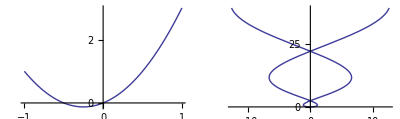

```mathematica
GraphicsRow[{
Plot[x+2x^2,{x,-1,1},ImageSize->150],
ParametricPlot[{2t Cos[t],t^2},{t,-2Pi,2Pi}],
GraphicsColumn[{Graphics[Circle[{0,0},2]],PolarPlot[t,{t,0,Pi},Axes->None]}]
},ImageSize->400]
```

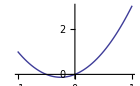

```mathematica
GraphicsColumn[{
Plot[x+2x^2,{x,-1,1},ImageSize->140],
GraphicsRow[{Graphics[Circle[{0,0},2]],PolarPlot[t,{t,0,Pi},Axes->None]}]
},ImageSize->150]
```

© 2015-2023 by David Wang, dwang@liberty.edu